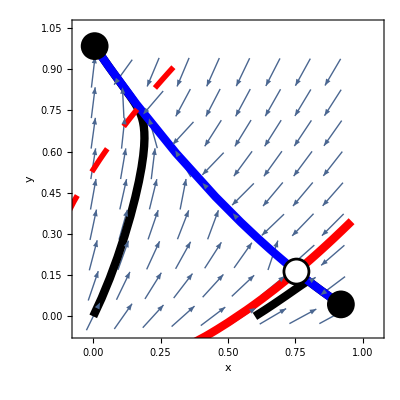

```mathematica
(* Separatrics for unstable phase *)
RR=2.1; BB=4;Aa = 2; Ab = 1;GG = 0.1;
f[x_,y_]=(1-x-y)*(Aa+BB*Aa*x)-GG*x - RR*x*y;
g[x_,y_]=(1-x-y)*(Ab+BB*Ab*y)-GG*y - RR*x*y;
ptRules1=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}]; 
eps = 1/10000; 
sol[{x0_,y0_,tmin_,tmax_}]:=NDSolveValue[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tmin,tmax}]; 
sep3=ParametricPlot[Evaluate@sol[{0.16302451135647034,0.7539264572310513+eps,-.9,0}],{t,-.9,0},PlotStyle->{Red,Dashing[0.05],Thickness[.01]}];
sep4=ParametricPlot[Evaluate@sol[{0.16302451135647034-eps,0.7539264572310513-eps,-40,0}],{t,-40,0},PlotStyle->{Red,Dashing[0.05],Thickness[.01]}];

(* Separatrics for stable phase *)
RR=2.1; BB=4;Aa = 1; Ab = 2;GG = 0.1;
f[x_,y_]=(1-x-y)*(Aa+BB*Aa*x)-GG*x - RR*x*y;
g[x_,y_]=(1-x-y)*(Ab+BB*Ab*y)-GG*y - RR*x*y;
vp=VectorPlot[{f[x,y],g[x,y]},{x,0,1},{y,0,1},VectorScale->{0.08,1,None},Axes->True,AxesLabel->{x,y},VectorPoints->10,VectorColorFunction->Hue[0,0,1]];
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,0,1},{y,0,1}];
ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}]; 
eps = 1/10000; 
sol[{x0_,y0_,tmin_,tmax_}]:=NDSolveValue[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,tmin,tmax}]; 
sep5=ParametricPlot[Evaluate@sol[{0.7539264572310446+eps,0.16302451135647505,0,40}],{t,0,40},PlotStyle->{Blue,Thickness[.015]}];
sep6=ParametricPlot[Evaluate@sol[{0.7539264572310446-eps,0.16302451135647505,0,40}],{t,0,40},PlotStyle->{Blue,Thickness[.015]}];
sep7=ParametricPlot[Evaluate@sol[{0.7539264572310446,0.16302451135647505+eps,-.9,0}],{t,-.9,0},PlotStyle->{Red,Thickness[.015]}];
sep8=ParametricPlot[Evaluate@sol[{0.7539264572310446-eps,0.16302451135647505-eps,-40,0}],{t,-40,0},PlotStyle->{Red,Thickness[.015]}];
trac1=ParametricPlot[Evaluate@sol[{0,0,0,100}],{t,0,100},PlotStyle->{Black,Thickness[.015]}];
trac2=ParametricPlot[Evaluate@sol[{0.6,0,0,100}],{t,0,100},PlotStyle->{Black,Thickness[.015]}];
Show[vp,trac1,trac2,sep5,sep6,sep7,sep8,sep3,sep4,Graphics[{Black,PointSize[0.05],Point[{x,y}]/.ptRules}],Graphics[{White,PointSize[0.04],Point[{x,y}]/.ptRules[[2]]}], LabelStyle->Directive[Black,Large]]
```